## Uppgift 1

```mathematica
countries={"Africa Eastern and Southern","Afghanistan","Africa Western and Central","Angola","Albania","Andorra","Arab World","United Arab Emirates","Argentina","Armenia","Antigua and Barbuda","Australia","Austria","Azerbaijan","Burundi","Belgium","Benin","Burkina Faso","Bangladesh","Bulgaria","Bahrain","Bahamas, The","Bosnia and Herzegovina","Belarus","Belize","Bolivia","Brazil","Barbados","Brunei Darussalam","Bhutan","Botswana","Central African Republic","Canada","Central Europe and the Baltics","Switzerland","Chile","China","Cote d'Ivoire","Cameroon","Congo, Dem. Rep.","Congo, Rep.","Colombia","Comoros","Cabo Verde","Costa Rica","Caribbean small states","Cuba","Cyprus","Czech Republic","Germany","Djibouti","Dominica","Denmark","Dominican Republic","Algeria","East Asia & Pacific (excluding high income)","Early-demographic dividend","East Asia & Pacific","Europe & Central Asia (excluding high income)","Europe & Central Asia","Ecuador","Egypt, Arab Rep.","Euro area","Eritrea","Spain","Estonia","Ethiopia","European Union","Fragile and conflict affected situations","Finland","Fiji","France","Micronesia, Fed. Sts.","Gabon","United Kingdom","Georgia","Ghana","Guinea","Gambia, The","Guinea-Bissau","Equatorial Guinea","Greece","Grenada","Guatemala","Guyana","High income","Honduras","Heavily indebted poor countries (HIPC)","Croatia","Haiti","Hungary","IBRD only","IDA & IBRD total","IDA total","IDA blend","Indonesia","IDA only","India","Ireland","Iran, Islamic Rep.","Iraq","Iceland","Israel","Italy","Jamaica","Jordan","Japan","Kazakhstan","Kenya","Kyrgyz Republic","Cambodia","Kiribati","St. Kitts and Nevis","Korea, Rep.","Kuwait","Latin America & Caribbean (excluding high income)","Lao PDR","Lebanon","Liberia","Libya","St. Lucia","Latin America & Caribbean","Least developed countries: UN classification","Low income","Liechtenstein","Sri Lanka","Lower middle income","Low & middle income","Lesotho","Late-demographic dividend","Lithuania","Luxembourg","Latvia","Morocco","Moldova","Madagascar","Maldives","Middle East & North Africa","Mexico","Marshall Islands","Middle income","North Macedonia","Mali","Malta","Myanmar","Middle East & North Africa (excluding high income)","Montenegro","Mongolia","Mozambique","Mauritania","Mauritius","Malawi","Malaysia","North America","Namibia","Niger","Nigeria","Nicaragua","Netherlands","Norway","Nepal","Nauru","New Zealand","OECD members","Oman","Other small states","Pakistan","Panama","Peru","Philippines","Palau","Papua New Guinea","Poland","Pre-demographic dividend","Korea, Dem. People's Rep.","Portugal","Paraguay","Pacific island small states","Post-demographic dividend","Qatar","Romania","Russian Federation","Rwanda","South Asia","Saudi Arabia","Sudan","Senegal","Singapore","Solomon Islands","Sierra Leone","El Salvador","Somalia","Serbia","Sub-Saharan Africa (excluding high income)","South Sudan","Sub-Saharan Africa","Small states","Sao Tome and Principe","Suriname","Slovak Republic","Slovenia","Sweden","Eswatini","Seychelles","Syrian Arab Republic","Chad","East Asia & Pacific (IDA & IBRD countries)","Europe & Central Asia (IDA & IBRD countries)","Togo","Thailand","Tajikistan","Turkmenistan","Latin America & the Caribbean (IDA & IBRD countries)","Timor-Leste","Middle East & North Africa (IDA & IBRD countries)","Tonga","South Asia (IDA & IBRD)","Sub-Saharan Africa (IDA & IBRD countries)","Trinidad and Tobago","Tunisia","Turkey","Tuvalu","Tanzania","Uganda","Ukraine","Upper middle income","Uruguay","United States","Uzbekistan","St. Vincent and the Grenadines","Venezuela, RB","Vietnam","Vanuatu","World","Samoa","Yemen, Rep.","South Africa","Zambia","Zimbabwe"};
```

```mathematica
co2emissions={600351.1333,7440,224380,27340,5560,460,1863603.727,200300,177410,5550,530,386620,63180,32020,590,93470,7910,4270,82760,41130,30750,2260,22540,59310,680,22710,427710,1250,7140,1380,8210,330,574400,676470,37480,86620,10313460,9910,8620,2200,3220,79490,260,620,8260,36920,24970,7230,102480,709540,490,180,33380,25120,151670,11907866.46,7400359.524,14810056.87,2949087.39,6142069.263,39530,246260,2207420,800,258340,16000,16280,2871000,771602.9297,44360,1900,309960,180,4610,358800,9460,16110,3120,570,310,6670,65290,300,18210,2440,12366368.33,9770,211980,16580,3330,46390,20938730,21860535.52,915178.5696,505410,583110,407199.3144,2434520,37110,629290,188140,2200,61970,324850,8510,24700,1106150,220450,18400,11000,11160,80,260,630870,89460,1408370,18790,27710,1320,58940,390,1689187.436,338640.0291,149413.7119,140,21630,5608350.968,21334207.73,2570,14912796.92,11590,9320,7630,66680,8590,3370,1910,2531611.759,472140,190,21177938.67,7370,5620,1550,32520,1470946.392,2520,21320,6640,4000,4130,1570,239620,5558099.304,4250,2290,130670,5210,151170,37350,12030,70,32210,11998460,73370,197072.5527,208370,10140,54280,142240,290,7460,312740,513004.5719,18120,49780,8420,3780,10935463.93,90170,74880,1607550,1080,2770040,514600,20200,9860,47360,370,1020,6810,690,45540,822805.4476,1380,823424.7218,237761.658,140,2080,33000,14050,36000,1090,620,27910,1070,11889820,3278021.798,2260,257860,7330,71730,1633250,640,1461080,190,2770040,823424.7218,17760,29980,412970,10,11580,6130,185370,15569855.45,6520,4981300,112090,280,138160,257860,180,34041045.97,320,9310,433250,7740,12270};
```

```mathematica
co2perCapita={0.933541201,0.200151071,0.515544239,0.887380364,1.939731563,5.97340536,4.438715965,20.7974984,3.987234198,1.880246268,5.504663385,15.47551649,7.146637625,3.221402183,0.05279463,8.179711061,0.688722324,0.216186485,0.512837314,5.854773434,19.59297584,5.86046391,6.781131607,6.2540208,1.775127848,2.000327663,2.041874199,4.360870779,16.64490862,1.829277992,3.64230522,0.070718706,15.49702527,6.597232486,4.401991044,4.624872245,7.405211347,0.395305384,0.341842908,0.026169263,0.613992586,1.600650618,0.312379103,1.140200528,1.652184053,5.017034408,2.202300094,6.079400502,9.640704998,8.558389812,0.510989933,2.513053919,5.761494164,2.363757648,3.591657418,5.720397083,2.27814572,6.361179651,7.07331348,6.690105957,2.3138123,2.502042142,6.454837567,0.231696216,5.5203504,12.103085,0.149050931,6.424038741,0.868444604,8.04275205,2.150561976,4.619241205,1.598011364,2.175272204,5.398708138,2.538541691,0.541201382,0.251323233,0.249989913,0.165394728,5.095625096,6.08317505,2.691814193,1.113969273,3.13219265,10.25453315,1.019032757,0.271687567,4.055928762,0.299374738,4.745506244,4.382903441,3.40988701,0.560235135,0.920386827,2.178461553,0.37549488,1.799825446,7.624325193,7.693012599,4.895195361,6.237224322,6.976403837,5.376374339,2.899634155,2.478595273,8.74225771,12.06196914,0.358028408,1.73973556,0.686777895,0.690595812,4.958236393,12.22459136,21.62272431,2.413939907,2.660908493,4.039707217,0.273917114,8.825249137,2.14415306,2.637362569,0.335389683,0.23673353,3.692177857,0.99815413,1.730955497,3.355676738,1.218975994,6.518254124,4.137005929,15.33020808,3.959165078,1.850726784,3.171832063,0.128320761,3.703674976,5.638657141,3.741477725,3.252756283,3.69823452,3.538239148,0.294583928,3.198316241,0.605492803,3.841040725,4.049968902,6.725098053,0.225115201,0.908407126,3.264040313,0.086533726,7.600220413,15.27087561,1.735898378,0.102037038,0.667110199,0.805815233,8.772823734,7.031361189,0.428179218,6.555534744,6.572664572,8.835263958,15.19212436,6.406682315,0.981820105,2.42765632,1.69681923,1.33369096,16.19116744,0.866804457,8.235472255,0.557925928,0.709208588,4.840612761,1.210453778,1.539504166,9.853587312,32.41563917,3.845132759,11.12661837,0.087790824,1.526651238,15.26878053,0.483235878,0.621912357,8.399134832,0.566740598,0.133330736,1.060625411,0.04597479,6.521922194,0.763112676,0.125729734,0.763618494,5.859845144,0.663406498,3.611192614,6.058635474,6.774695332,3.538009127,0.959275668,6.407474008,1.647087511,0.069131598,5.782778671,7.141751179,0.286471389,3.714039204,0.80541954,12.25964817,2.614462991,0.504741813,3.861347119,1.841103111,1.526651238,0.763618494,12.77844012,2.592258865,5.01541837,0.86918731,0.205634733,0.143462178,4.154180631,6.261836804,1.890244079,15.24087458,3.401191282,2.540604301,4.782754887,2.698805922,0.615016657,4.483523912,1.631587535,0.326681763,7.496644895,0.446065443,0.849792905};
```

```mathematica
BarChart[co2perCapita,PlotLabel->"CO2 Utsläpp per capita", BarOrigin ->Left,ChartLabels->Placed[countries,Before], BarSpacing->None,AspectRatio->Full, ImageSize-> {1000,2500}, LabelingSize->250, AxesLabel->{"Länder","CO2 Utsläpp per capita"}];
```

```mathematica
totaltutsläpp = Table[{co2emissions[[x]],countries[[x]]},{x,1,239}];
```

```mathematica
sortUtsläpp= Sort[totaltutsläpp];
```

```mathematica
{3.404104597*^7,"World"};
world={3.404104597*^7}
```

{3.4041×10^7}

```mathematica
fdata={10313460,4981300,2434520,1607550,1106150};
```

```mathematica
rest=world-Total[fdata]
```

{1.35981×10^7}

```mathematica
fdataNew={10313460,4981300,2434520,1607550,1106150,3.404104597*^7};
```

```mathematica
fnamn={China,"United States",India,"Russian Federation",Japan,"resten av världen"};
```

```mathematica
PieChart[{fdataNew}, ChartLegends->{fnamn}, ChartStyle->"DarkRainbow",PlotLabel->" CO2 Utsläpp för de 5 länder som släpper ut mest och resten av världen", ImageSize->{500, 700}];
```

## Analysera data

### 1.

```mathematica
totalt={{1990.,98462.371847116},{1991.,98987.38143285},{1992.,99813.54908523199},{1993.,100216.423316547},{1994.,101537.18489717401},{1995.,103296.25934793001},{1996.,106154.70010584098},{1997.,107376.31135546902},{1998.,108022.57284627101},{1999.,109856.69807370701},{2000.,112416.258116246},{2001.,113610.635952175},{2002.,115901.223848704},{2003.,119930.15013616001},{2004.,124960.08846344402},{2005.,128897.75152416898},{2006.,132297.06634468702},{2007.,136405.679742778},{2008.,137662.43593741},{2009.,135324.15543267998},{2010.,141265.10288404},{2011.,144422.53459229},{2012.,146106.05926769998},{2013.,148234.8407671},{2014.,149077.14748530003},{2015.,149790.2224058},{2016.,151341.68784990002},{2017.,153595.6630277}};
```

```mathematica
tot1=Table[totalt[[x,2]],{x,1,28}]
```

{98462.4,98987.4,99813.5,100216.,101537.,103296.,106155.,107376.,108023.,109857.,112416.,113611.,115901.,119930.,124960.,128898.,132297.,136406.,137662.,135324.,141265.,144423.,146106.,148235.,149077.,149790.,151342.,153596.}

```mathematica
model=a Exp[-k t]; (*funktion för exponetial funktion*)
```

```mathematica
fit= FindFit[tot1,model,{a,k},t]
```

{a→93601.1,k→-0.0186746}

```mathematica
modelf=Function[{t},Evaluate[model/.fit]]
```

Function[{t},93601.1 ⅇ^(0.0186746 t)]

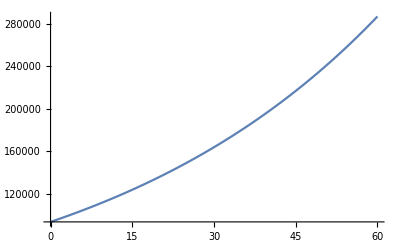

```mathematica
Plot[modelf[t],{t,0,60},Epilog->Map[Point,totalt]]
```

```mathematica
{a1,b1}={a,b}/.FindFit[totalt,{a(t-1990)+b},{a,b},t]
```

{2314.87,92855.}

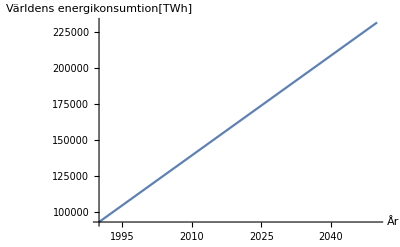

```mathematica
p1=Plot[a1(t-1990)+b1,{t,1990,2050}, AxesLabel->{"År","Världens energikonsumtion[TWh]"}]
```

### 2.

```mathematica
andrafornybara={{1990.,116.4628246},{1991.,121.4122701},{1992.,130.3448548},{1993.,134.7069628},{1994.,139.8004029},{1995.,145.5958811},{1996.,149.6884804},{1997.,160.9528063},{1998.,168.4548712},{1999.,177.1371664},{2000.,185.2722028},{2001.,191.0179267},{2002.,205.6996386},{2003.,217.2027959},{2004.,234.3682046},{2005.,254.3922875},{2006.,271.7633551},{2007.,294.2977297},{2008.,314.3656167},{2009.,338.2157334},{2010.,378.0383427},{2011.,397.4546676},{2012.,430.3624386},{2013.,463.9825019},{2014.,504.3899227},{2015.,538.2067786},{2016.,556.9861292},{2017.,586.1710901}};
```

```mathematica
vatten={{1990.,2161.045291},{1991.,2213.110915},{1992.,2211.503167},{1993.,2344.266136},{1994.,2359.685227},{1995.,2488.983207},{1996.,2523.481143},{1997.,2569.633113},{1998.,2590.551798},{1999.,2608.338262},{2000.,2654.953445},{2001.,2586.668594},{2002.,2633.835653},{2003.,2629.430399},{2004.,2808.226932},{2005.,2918.064831},{2006.,3030.307944},{2007.,3079.79887},{2008.,3263.589026},{2009.,3253.601171},{2010.,3435.905581},{2011.,3503.227091},{2012.,3671.297583},{2013.,3797.954118},{2014.,3887.930335},{2015.,3891.408797},{2016.,4036.073668},{2017.,4059.868393}};
```

```mathematica
vind={{1990.,3.632470516},{1991.,4.086706675},{1992.,4.733212019},{1993.,5.697568819},{1994.,7.122929844},{1995.,8.261923444},{1996.,9.204610762},{1997.,12.01757667},{1998.,15.91490057},{1999.,21.21534431},{2000.,31.41996387},{2001.,38.39098735},{2002.,52.33180737},{2003.,62.91691456},{2004.,85.11605376},{2005.,104.0868359},{2006.,132.8592792},{2007.,170.6860872},{2008.,220.5696719},{2009.,275.9292658},{2010.,341.5652412},{2011.,436.8034429},{2012.,523.8148612},{2013.,645.7219776},{2014.,712.4070431},{2015.,831.8262454},{2016.,959.4687163},{2017.,1122.74585}};
```

```mathematica
sol={{1990.,0.},{1991.,0.505223075},{1992.,0.468615413},{1993.,0.556737928},{1994.,0.60006443},{1995.,0.640874386},{1996.,0.705278679},{1997.,0.756655499},{1998.,0.880289501},{1999.,0.965823997},{2000.,1.177935576},{2001.,1.463956125},{2002.,1.831247734},{2003.,2.3293707},{2004.,3.054656084},{2005.,4.249617769},{2006.,5.818328387},{2007.,7.864870878},{2008.,12.72162081},{2009.,21.09259048},{2010.,33.82948514},{2011.,65.21188479},{2012.,100.9252749},{2013.,139.0442186},{2014.,197.6716635},{2015.,260.0058008},{2016.,328.1826964},{2017.,442.6183606}};
```

```mathematica
totFörnybar=Table[{andrafornybara[[x,1]],andrafornybara[[x,2]]+vatten[[x,2]]+vind[[x,2]]+sol[[x,2]]},{x,1,28}]
```

{{1990.,2281.14},{1991.,2339.12},{1992.,2347.05},{1993.,2485.23},{1994.,2507.21},{1995.,2643.48},{1996.,2683.08},{1997.,2743.36},{1998.,2775.8},{1999.,2807.66},{2000.,2872.82},{2001.,2817.54},{2002.,2893.7},{2003.,2911.88},{2004.,3130.77},{2005.,3280.79},{2006.,3440.75},{2007.,3552.65},{2008.,3811.25},{2009.,3888.84},{2010.,4189.34},{2011.,4402.7},{2012.,4726.4},{2013.,5046.7},{2014.,5302.4},{2015.,5521.45},{2016.,5880.71},{2017.,6211.4}}

```mathematica
olja={{1990.,37736.94729},{1991.,37763.14824},{1992.,38422.53103},{1993.,38179.42324},{1994.,39021.80173},{1995.,39555.43054},{1996.,40480.1731},{1997.,41544.67299},{1998.,41768.48384},{1999.,42510.09274},{2000.,43038.62001},{2001.,43421.10755},{2002.,43796.55068},{2003.,44803.21017},{2004.,46503.96733},{2005.,47115.72728},{2006.,47732.19992},{2007.,48471.73162},{2008.,48250.64229},{2009.,47422.36853},{2010.,48949.72046},{2011.,49455.27172},{2012.,50065.86499},{2013.,50698.38455},{2014.,51109.97172},{2015.,52053.27008},{2016.,53001.86598},{2017.,53752.27638}};
```

### 3.